```mathematica
%%%%%%%%%
l: SOC 1ueV;tau:5ueV;u:3meV;
%%%%%%%%%%%%
```

```mathematica
g=1.35;muB=9.27 10^(-24);B=0.015;ET=-g muB B;l=0.1 1.6 10^(-19) 10^(-6)/(hbar/2);tau=5 1.6 10^(-19) 10^(-6);u=3000 1.6 10^(-19) 10^(-6);hbar=1.055×10^(-34);
```

```mathematica
Es[eps_]=1/2(u+eps-Sqrt[8 tau^2+(u+eps)^2]);Delta[eps_]=(Es[eps]-ET)/2 /(hbar/2);eps0=-3050 1.6 10^(-19) 10^(-6);epstf=-2800 1.6 10^(-19) 10^(-6);dd=(Delta[epstf]-Delta[eps0])/10000000;c1=1/2Sum[1/Norm[((l)^2+(Deltax)^2)^1.5/(l)]dd,{Deltax,Delta[eps0],Delta[epstf],dd}];
```

```mathematica
c1
```

3.25952×10^-9

```mathematica
Clear[DF];DF={};Clear[DFs];DFs={};
```

```mathematica
Do[c=c1/tf0;f[s_]=c1 2 Norm[ (Delta0[s]^2+l^2)^1.5/(l )];Sol=NDSolve[{Delta0'[s]==f[s],Delta0[0]==Delta[eps0]},Delta0,{s,0,1},MaxSteps->∞];Deltas[s_]=Delta0[s]/.Sol;Deltat[t_]=Deltas[t/tf0 ];Soleps=Solve[Deltat[t]==(Est[t]-ET)/2 /(hbar/2),Est[t]];Est0[t_]=Est[t]/.Soleps[[1]];Clear[Deps];Deps={};Clear[Deps0];Deps0={};Do[Solf=NSolve[Est0[t0]==1/2(u+eps-Sqrt[8 tau^2+(u+eps)^2]),eps];Deps=Append[Deps,{t0,eps/.Solf[[1]]}];Deps0=Append[Deps0,{t0/tf0,(eps/.Solf[[1]])/(1.6 10^(-22))}],{t0,0,tf0,tf0/1000}];feps=Interpolation[Deps];f1[t_]=feps[t];fEs[t_]=1/2(u+f1[t]-Sqrt[8 tau^2+(u+f1[t])^2]);fDelta[t_]=(fEs[t]-ET)/2 /(hbar/2);s2=NDSolve[{I  h1'[t]==fDelta[t]/2 h1[t]+ l/2  h2[t],
I  h2'[t]== l/2 h1[t]-fDelta[t]/2 h2[t],
h1[0]==1,h2[0]==0},{h1[t],h2[t]},{t,0,tf0},MaxSteps->∞];
sh10[t_]=Abs[h1[t]/.s2]^2;
sh20[t_]=Abs[h2[t]/.s2]^2;F=sh20[tf0][[1]];DF=Append[DF,{tf0,F}];DFs=Append[DFs,{tf0/(10^(-9)),F}],{tf0,0.1 10^(-9),30 10^(-9),0.2 10^(-9)}]
```

```mathematica
Deps0
```

{{0.,-3000.},{0.00565,-2999.31},{0.0113,-2998.77},{0.01695,-2998.33},{0.0226,-2997.97},{0.02825,-2997.67},{0.0339,-2997.4},{0.03955,-2997.16},{0.0452,-2996.96},{0.05085,-2996.77},{0.0565,-2996.6},{0.06215,-2996.44},{0.0678,-2996.3},{0.07345,-2996.17},{0.0791,-2996.05},{0.08475,-2995.94},{0.0904,-2995.83},{0.09605,-2995.73},{0.1017,-2995.64},{0.10735,-2995.55},{0.113,-2995.47},{0.11865,-2995.39},{0.1243,-2995.32},{0.12995,-2995.25},{0.1356,-2995.18},{0.14125,-2995.11},{0.1469,-2995.05},{0.15255,-2994.99},{0.1582,-2994.94},{0.16385,-2994.88},{0.1695,-2994.83},{0.17515,-2994.78},{0.1808,-2994.73},{0.18645,-2994.68},{0.1921,-2994.64},{0.19775,-2994.59},{0.2034,-2994.55},{0.20905,-2994.51},{0.2147,-2994.47},{0.22035,-2994.43},{0.226,-2994.4},{0.23165,-2994.36},{0.2373,-2994.32},{0.24295,-2994.29},{0.2486,-2994.26},{0.25425,-2994.22},{0.2599,-2994.19},{0.26555,-2994.16},{0.2712,-2994.13},{0.27685,-2994.1},{0.2825,-2994.07},{0.28815,-2994.05},{0.2938,-2994.02},{0.29945,-2993.99},{0.3051,-2993.96},{0.31075,-2993.94},{0.3164,-2993.91},{0.32205,-2993.89},{0.3277,-2993.87},{0.33335,-2993.84},{0.339,-2993.82},{0.34465,-2993.8},{0.3503,-2993.77},{0.35595,-2993.75},{0.3616,-2993.73},{0.36725,-2993.71},{0.3729,-2993.69},{0.37855,-2993.67},{0.3842,-2993.65},{0.38985,-2993.63},{0.3955,-2993.61},{0.40115,-2993.59},{0.4068,-2993.57},{0.41245,-2993.56},{0.4181,-2993.54},{0.42375,-2993.52},{0.4294,-2993.5},{0.43505,-2993.49},{0.4407,-2993.47},{0.44635,-2993.45},{0.452,-2993.44},{0.45765,-2993.42},{0.4633,-2993.4},{0.46895,-2993.39},{0.4746,-2993.37},{0.48025,-2993.36},{0.4859,-2993.34},{0.49155,-2993.33},{0.4972,-2993.31},{0.50285,-2993.3},{0.5085,-2993.28},{0.51415,-2993.27},{0.5198,-2993.26},{0.52545,-2993.24},{0.5311,-2993.23},{0.53675,-2993.22},{0.5424,-2993.2},{0.54805,-2993.19},{0.5537,-2993.18},{0.55935,-2993.16},{0.565,-2993.15},{0.57065,-2993.14},{0.5763,-2993.13},{0.58195,-2993.11},{0.5876,-2993.1},{0.59325,-2993.09},{0.5989,-2993.08},{0.60455,-2993.07},{0.6102,-2993.06},{0.61585,-2993.04},{0.6215,-2993.03},{0.62715,-2993.02},{0.6328,-2993.01},{0.63845,-2993.},{0.6441,-2992.99},{0.64975,-2992.98},{0.6554,-2992.97},{0.66105,-2992.96},{0.6667,-2992.95},{0.67235,-2992.94},{0.678,-2992.93},{0.68365,-2992.92},{0.6893,-2992.91},{0.69495,-2992.9},{0.7006,-2992.89},{0.70625,-2992.88},{0.7119,-2992.87},{0.71755,-2992.86},{0.7232,-2992.85},{0.72885,-2992.84},{0.7345,-2992.83},{0.74015,-2992.82},{0.7458,-2992.81},{0.75145,-2992.8},{0.7571,-2992.79},{0.76275,-2992.78},{0.7684,-2992.78},{0.77405,-2992.77},{0.7797,-2992.76},{0.78535,-2992.75},{0.791,-2992.74},{0.79665,-2992.73},{0.8023,-2992.72},{0.80795,-2992.72},{0.8136,-2992.71},{0.81925,-2992.7},{0.8249,-2992.69},{0.83055,-2992.68},{0.8362,-2992.68},{0.84185,-2992.67},{0.8475,-2992.66},{0.85315,-2992.65},{0.8588,-2992.64},{0.86445,-2992.64},{0.8701,-2992.63},{0.87575,-2992.62},{0.8814,-2992.61},{0.88705,-2992.61},{0.8927,-2992.6},{0.89835,-2992.59},{0.904,-2992.58},{0.90965,-2992.58},{0.9153,-2992.57},{0.92095,-2992.56},{0.9266,-2992.55},{0.93225,-2992.55},{0.9379,-2992.54},{0.94355,-2992.53},{0.9492,-2992.53},{0.95485,-2992.52},{0.9605,-2992.51},{0.96615,-2992.5},{0.9718,-2992.5},{0.97745,-2992.49},{0.9831,-2992.48},{0.98875,-2992.48},{0.9944,-2992.47},{1.00005,-2992.46},{1.0057,-2992.46},{1.01135,-2992.45},{1.017,-2992.44},{1.02265,-2992.44},{1.0283,-2992.43},{1.03395,-2992.43},{1.0396,-2992.42},{1.04525,-2992.41},{1.0509,-2992.41},{1.05655,-2992.4},{1.0622,-2992.39},{1.06785,-2992.39},{1.0735,-2992.38},{1.07915,-2992.38},{1.0848,-2992.37},{1.09045,-2992.36},{1.0961,-2992.36},{1.10175,-2992.35},{1.1074,-2992.34},{1.11305,-2992.34},{1.1187,-2992.33},{1.12435,-2992.33},{1.13,-2992.32},{1.13565,-2992.32},{1.1413,-2992.31},{1.14695,-2992.3},{1.1526,-2992.3},{1.15825,-2992.29},{1.1639,-2992.29},{1.16955,-2992.28},{1.1752,-2992.28},{1.18085,-2992.27},{1.1865,-2992.26},{1.19215,-2992.26},{1.1978,-2992.25},{1.20345,-2992.25},{1.2091,-2992.24},{1.21475,-2992.24},{1.2204,-2992.23},{1.22605,-2992.23},{1.2317,-2992.22},{1.23735,-2992.21},{1.243,-2992.21},{1.24865,-2992.2},{1.2543,-2992.2},{1.25995,-2992.19},{1.2656,-2992.19},{1.27125,-2992.18},{1.2769,-2992.18},{1.28255,-2992.17},{1.2882,-2992.17},{1.29385,-2992.16},{1.2995,-2992.16},{1.30515,-2992.15},{1.3108,-2992.15},{1.31645,-2992.14},{1.3221,-2992.14},{1.32775,-2992.13},{1.3334,-2992.13},{1.33905,-2992.12},{1.3447,-2992.12},{1.35035,-2992.11},{1.356,-2992.11},{1.36165,-2992.1},{1.3673,-2992.1},{1.37295,-2992.09},{1.3786,-2992.09},{1.38425,-2992.08},{1.3899,-2992.08},{1.39555,-2992.07},{1.4012,-2992.07},{1.40685,-2992.06},{1.4125,-2992.06},{1.41815,-2992.05},{1.4238,-2992.05},{1.42945,-2992.04},{1.4351,-2992.04},{1.44075,-2992.04},{1.4464,-2992.03},{1.45205,-2992.03},{1.4577,-2992.02},{1.46335,-2992.02},{1.469,-2992.01},{1.47465,-2992.01},{1.4803,-2992.},{1.48595,-2992.},{1.4916,-2991.99},{1.49725,-2991.99},{1.5029,-2991.98},{1.50855,-2991.98},{1.5142,-2991.98},{1.51985,-2991.97},{1.5255,-2991.97},{1.53115,-2991.96},{1.5368,-2991.96},{1.54245,-2991.95},{1.5481,-2991.95},{1.55375,-2991.94},{1.5594,-2991.94},{1.56505,-2991.94},{1.5707,-2991.93},{1.57635,-2991.93},{1.582,-2991.92},{1.58765,-2991.92},{1.5933,-2991.91},{1.59895,-2991.91},{1.6046,-2991.91},{1.61025,-2991.9},{1.6159,-2991.9},{1.62155,-2991.89},{1.6272,-2991.89},{1.63285,-2991.88},{1.6385,-2991.88},{1.64415,-2991.88},{1.6498,-2991.87},{1.65545,-2991.87},{1.6611,-2991.86},{1.66675,-2991.86},{1.6724,-2991.86},{1.67805,-2991.85},{1.6837,-2991.85},{1.68935,-2991.84},{1.695,-2991.84},{1.70065,-2991.83},{1.7063,-2991.83},{1.71195,-2991.83},{1.7176,-2991.82},{1.72325,-2991.82},{1.7289,-2991.81},{1.73455,-2991.81},{1.7402,-2991.81},{1.74585,-2991.8},{1.7515,-2991.8},{1.75715,-2991.79},{1.7628,-2991.79},{1.76845,-2991.79},{1.7741,-2991.78},{1.77975,-2991.78},{1.7854,-2991.77},{1.79105,-2991.77},{1.7967,-2991.77},{1.80235,-2991.76},{1.808,-2991.76},{1.81365,-2991.75},{1.8193,-2991.75},{1.82495,-2991.75},{1.8306,-2991.74},{1.83625,-2991.74},{1.8419,-2991.74},{1.84755,-2991.73},{1.8532,-2991.73},{1.85885,-2991.72},{1.8645,-2991.72},{1.87015,-2991.72},{1.8758,-2991.71},{1.88145,-2991.71},{1.8871,-2991.7},{1.89275,-2991.7},{1.8984,-2991.7},{1.90405,-2991.69},{1.9097,-2991.69},{1.91535,-2991.69},{1.921,-2991.68},{1.92665,-2991.68},{1.9323,-2991.67},{1.93795,-2991.67},{1.9436,-2991.67},{1.94925,-2991.66},{1.9549,-2991.66},{1.96055,-2991.66},{1.9662,-2991.65},{1.97185,-2991.65},{1.9775,-2991.64},{1.98315,-2991.64},{1.9888,-2991.64},{1.99445,-2991.63},{2.0001,-2991.63},{2.00575,-2991.63},{2.0114,-2991.62},{2.01705,-2991.62},{2.0227,-2991.61},{2.02835,-2991.61},{2.034,-2991.61},{2.03965,-2991.6},{2.0453,-2991.6},{2.05095,-2991.6},{2.0566,-2991.59},{2.06225,-2991.59},{2.0679,-2991.59},{2.07355,-2991.58},{2.0792,-2991.58},{2.08485,-2991.57},{2.0905,-2991.57},{2.09615,-2991.57},{2.1018,-2991.56},{2.10745,-2991.56},{2.1131,-2991.56},{2.11875,-2991.55},{2.1244,-2991.55},{2.13005,-2991.55},{2.1357,-2991.54},{2.14135,-2991.54},{2.147,-2991.54},{2.15265,-2991.53},{2.1583,-2991.53},{2.16395,-2991.52},{2.1696,-2991.52},{2.17525,-2991.52},{2.1809,-2991.51},{2.18655,-2991.51},{2.1922,-2991.51},{2.19785,-2991.5},{2.2035,-2991.5},{2.20915,-2991.5},{2.2148,-2991.49},{2.22045,-2991.49},{2.2261,-2991.49},{2.23175,-2991.48},{2.2374,-2991.48},{2.24305,-2991.48},{2.2487,-2991.47},{2.25435,-2991.47},{2.26,-2991.46},{2.26565,-2991.46},{2.2713,-2991.46},{2.27695,-2991.45},{2.2826,-2991.45},{2.28825,-2991.45},{2.2939,-2991.44},{2.29955,-2991.44},{2.3052,-2991.44},{2.31085,-2991.43},{2.3165,-2991.43},{2.32215,-2991.43},{2.3278,-2991.42},{2.33345,-2991.42},{2.3391,-2991.42},{2.34475,-2991.41},{2.3504,-2991.41},{2.35605,-2991.41},{2.3617,-2991.4},{2.36735,-2991.4},{2.373,-2991.4},{2.37865,-2991.39},{2.3843,-2991.39},{2.38995,-2991.39},{2.3956,-2991.38},{2.40125,-2991.38},{2.4069,-2991.37},{2.41255,-2991.37},{2.4182,-2991.37},{2.42385,-2991.36},{2.4295,-2991.36},{2.43515,-2991.36},{2.4408,-2991.35},{2.44645,-2991.35},{2.4521,-2991.35},{2.45775,-2991.34},{2.4634,-2991.34},{2.46905,-2991.34},{2.4747,-2991.33},{2.48035,-2991.33},{2.486,-2991.33},{2.49165,-2991.32},{2.4973,-2991.32},{2.50295,-2991.32},{2.5086,-2991.31},{2.51425,-2991.31},{2.5199,-2991.31},{2.52555,-2991.3},{2.5312,-2991.3},{2.53685,-2991.3},{2.5425,-2991.29},{2.54815,-2991.29},{2.5538,-2991.29},{2.55945,-2991.28},{2.5651,-2991.28},{2.57075,-2991.28},{2.5764,-2991.27},{2.58205,-2991.27},{2.5877,-2991.27},{2.59335,-2991.26},{2.599,-2991.26},{2.60465,-2991.26},{2.6103,-2991.25},{2.61595,-2991.25},{2.6216,-2991.25},{2.62725,-2991.24},{2.6329,-2991.24},{2.63855,-2991.24},{2.6442,-2991.23},{2.64985,-2991.23},{2.6555,-2991.23},{2.66115,-2991.22},{2.6668,-2991.22},{2.67245,-2991.22},{2.6781,-2991.21},{2.68375,-2991.21},{2.6894,-2991.21},{2.69505,-2991.2},{2.7007,-2991.2},{2.70635,-2991.19},{2.712,-2991.19},{2.71765,-2991.19},{2.7233,-2991.18},{2.72895,-2991.18},{2.7346,-2991.18},{2.74025,-2991.17},{2.7459,-2991.17},{2.75155,-2991.17},{2.7572,-2991.16},{2.76285,-2991.16},{2.7685,-2991.16},{2.77415,-2991.15},{2.7798,-2991.15},{2.78545,-2991.15},{2.7911,-2991.14},{2.79675,-2991.14},{2.8024,-2991.14},{2.80805,-2991.13},{2.8137,-2991.13},{2.81935,-2991.13},{2.825,-2991.12},{2.83065,-2991.12},{2.8363,-2991.12},{2.84195,-2991.11},{2.8476,-2991.11},{2.85325,-2991.11},{2.8589,-2991.1},{2.86455,-2991.1},{2.8702,-2991.1},{2.87585,-2991.09},{2.8815,-2991.09},{2.88715,-2991.09},{2.8928,-2991.08},{2.89845,-2991.08},{2.9041,-2991.08},{2.90975,-2991.07},{2.9154,-2991.07},{2.92105,-2991.07},{2.9267,-2991.06},{2.93235,-2991.06},{2.938,-2991.06},{2.94365,-2991.05},{2.9493,-2991.05},{2.95495,-2991.05},{2.9606,-2991.04},{2.96625,-2991.04},{2.9719,-2991.04},{2.97755,-2991.03},{2.9832,-2991.03},{2.98885,-2991.02},{2.9945,-2991.02},{3.00015,-2991.02},{3.0058,-2991.01},{3.01145,-2991.01},{3.0171,-2991.01},{3.02275,-2991.},{3.0284,-2991.},{3.03405,-2991.},{3.0397,-2990.99},{3.04535,-2990.99},{3.051,-2990.99},{3.05665,-2990.98},{3.0623,-2990.98},{3.06795,-2990.98},{3.0736,-2990.97},{3.07925,-2990.97},{3.0849,-2990.97},{3.09055,-2990.96},{3.0962,-2990.96},{3.10185,-2990.96},{3.1075,-2990.95},{3.11315,-2990.95},{3.1188,-2990.95},{3.12445,-2990.94},{3.1301,-2990.94},{3.13575,-2990.93},{3.1414,-2990.93},{3.14705,-2990.93},{3.1527,-2990.92},{3.15835,-2990.92},{3.164,-2990.92},{3.16965,-2990.91},{3.1753,-2990.91},{3.18095,-2990.91},{3.1866,-2990.9},{3.19225,-2990.9},{3.1979,-2990.9},{3.20355,-2990.89},{3.2092,-2990.89},{3.21485,-2990.88},{3.2205,-2990.88},{3.22615,-2990.88},{3.2318,-2990.87},{3.23745,-2990.87},{3.2431,-2990.87},{3.24875,-2990.86},{3.2544,-2990.86},{3.26005,-2990.86},{3.2657,-2990.85},{3.27135,-2990.85},{3.277,-2990.85},{3.28265,-2990.84},{3.2883,-2990.84},{3.29395,-2990.83},{3.2996,-2990.83},{3.30525,-2990.83},{3.3109,-2990.82},{3.31655,-2990.82},{3.3222,-2990.82},{3.32785,-2990.81},{3.3335,-2990.81},{3.33915,-2990.81},{3.3448,-2990.8},{3.35045,-2990.8},{3.3561,-2990.79},{3.36175,-2990.79},{3.3674,-2990.79},{3.37305,-2990.78},{3.3787,-2990.78},{3.38435,-2990.78},{3.39,-2990.77},{3.39565,-2990.77},{3.4013,-2990.76},{3.40695,-2990.76},{3.4126,-2990.76},{3.41825,-2990.75},{3.4239,-2990.75},{3.42955,-2990.75},{3.4352,-2990.74},{3.44085,-2990.74},{3.4465,-2990.73},{3.45215,-2990.73},{3.4578,-2990.73},{3.46345,-2990.72},{3.4691,-2990.72},{3.47475,-2990.72},{3.4804,-2990.71},{3.48605,-2990.71},{3.4917,-2990.7},{3.49735,-2990.7},{3.503,-2990.7},{3.50865,-2990.69},{3.5143,-2990.69},{3.51995,-2990.68},{3.5256,-2990.68},{3.53125,-2990.68},{3.5369,-2990.67},{3.54255,-2990.67},{3.5482,-2990.67},{3.55385,-2990.66},{3.5595,-2990.66},{3.56515,-2990.65},{3.5708,-2990.65},{3.57645,-2990.65},{3.5821,-2990.64},{3.58775,-2990.64},{3.5934,-2990.63},{3.59905,-2990.63},{3.6047,-2990.63},{3.61035,-2990.62},{3.616,-2990.62},{3.62165,-2990.61},{3.6273,-2990.61},{3.63295,-2990.61},{3.6386,-2990.6},{3.64425,-2990.6},{3.6499,-2990.59},{3.65555,-2990.59},{3.6612,-2990.59},{3.66685,-2990.58},{3.6725,-2990.58},{3.67815,-2990.57},{3.6838,-2990.57},{3.68945,-2990.56},{3.6951,-2990.56},{3.70075,-2990.56},{3.7064,-2990.55},{3.71205,-2990.55},{3.7177,-2990.54},{3.72335,-2990.54},{3.729,-2990.54},{3.73465,-2990.53},{3.7403,-2990.53},{3.74595,-2990.52},{3.7516,-2990.52},{3.75725,-2990.51},{3.7629,-2990.51},{3.76855,-2990.51},{3.7742,-2990.5},{3.77985,-2990.5},{3.7855,-2990.49},{3.79115,-2990.49},{3.7968,-2990.48},{3.80245,-2990.48},{3.8081,-2990.48},{3.81375,-2990.47},{3.8194,-2990.47},{3.82505,-2990.46},{3.8307,-2990.46},{3.83635,-2990.45},{3.842,-2990.45},{3.84765,-2990.44},{3.8533,-2990.44},{3.85895,-2990.44},{3.8646,-2990.43},{3.87025,-2990.43},{3.8759,-2990.42},{3.88155,-2990.42},{3.8872,-2990.41},{3.89285,-2990.41},{3.8985,-2990.4},{3.90415,-2990.4},{3.9098,-2990.4},{3.91545,-2990.39},{3.9211,-2990.39},{3.92675,-2990.38},{3.9324,-2990.38},{3.93805,-2990.37},{3.9437,-2990.37},{3.94935,-2990.36},{3.955,-2990.36},{3.96065,-2990.35},{3.9663,-2990.35},{3.97195,-2990.34},{3.9776,-2990.34},{3.98325,-2990.33},{3.9889,-2990.33},{3.99455,-2990.32},{4.0002,-2990.32},{4.00585,-2990.31},{4.0115,-2990.31},{4.01715,-2990.31},{4.0228,-2990.3},{4.02845,-2990.3},{4.0341,-2990.29},{4.03975,-2990.29},{4.0454,-2990.28},{4.05105,-2990.28},{4.0567,-2990.27},{4.06235,-2990.27},{4.068,-2990.26},{4.07365,-2990.26},{4.0793,-2990.25},{4.08495,-2990.25},{4.0906,-2990.24},{4.09625,-2990.23},{4.1019,-2990.23},{4.10755,-2990.22},{4.1132,-2990.22},{4.11885,-2990.21},{4.1245,-2990.21},{4.13015,-2990.2},{4.1358,-2990.2},{4.14145,-2990.19},{4.1471,-2990.19},{4.15275,-2990.18},{4.1584,-2990.18},{4.16405,-2990.17},{4.1697,-2990.17},{4.17535,-2990.16},{4.181,-2990.16},{4.18665,-2990.15},{4.1923,-2990.14},{4.19795,-2990.14},{4.2036,-2990.13},{4.20925,-2990.13},{4.2149,-2990.12},{4.22055,-2990.12},{4.2262,-2990.11},{4.23185,-2990.11},{4.2375,-2990.1},{4.24315,-2990.09},{4.2488,-2990.09},{4.25445,-2990.08},{4.2601,-2990.08},{4.26575,-2990.07},{4.2714,-2990.06},{4.27705,-2990.06},{4.2827,-2990.05},{4.28835,-2990.05},{4.294,-2990.04},{4.29965,-2990.03},{4.3053,-2990.03},{4.31095,-2990.02},{4.3166,-2990.02},{4.32225,-2990.01},{4.3279,-2990.},{4.33355,-2990.},{4.3392,-2989.99},{4.34485,-2989.99},{4.3505,-2989.98},{4.35615,-2989.97},{4.3618,-2989.97},{4.36745,-2989.96},{4.3731,-2989.95},{4.37875,-2989.95},{4.3844,-2989.94},{4.39005,-2989.93},{4.3957,-2989.93},{4.40135,-2989.92},{4.407,-2989.92},{4.41265,-2989.91},{4.4183,-2989.9},{4.42395,-2989.9},{4.4296,-2989.89},{4.43525,-2989.88},{4.4409,-2989.87},{4.44655,-2989.87},{4.4522,-2989.86},{4.45785,-2989.85},{4.4635,-2989.85},{4.46915,-2989.84},{4.4748,-2989.83},{4.48045,-2989.83},{4.4861,-2989.82},{4.49175,-2989.81},{4.4974,-2989.8},{4.50305,-2989.8},{4.5087,-2989.79},{4.51435,-2989.78},{4.52,-2989.78},{4.52565,-2989.77},{4.5313,-2989.76},{4.53695,-2989.75},{4.5426,-2989.75},{4.54825,-2989.74},{4.5539,-2989.73},{4.55955,-2989.72},{4.5652,-2989.71},{4.57085,-2989.71},{4.5765,-2989.7},{4.58215,-2989.69},{4.5878,-2989.68},{4.59345,-2989.67},{4.5991,-2989.67},{4.60475,-2989.66},{4.6104,-2989.65},{4.61605,-2989.64},{4.6217,-2989.63},{4.62735,-2989.62},{4.633,-2989.62},{4.63865,-2989.61},{4.6443,-2989.6},{4.64995,-2989.59},{4.6556,-2989.58},{4.66125,-2989.57},{4.6669,-2989.56},{4.67255,-2989.56},{4.6782,-2989.55},{4.68385,-2989.54},{4.6895,-2989.53},{4.69515,-2989.52},{4.7008,-2989.51},{4.70645,-2989.5},{4.7121,-2989.49},{4.71775,-2989.48},{4.7234,-2989.47},{4.72905,-2989.46},{4.7347,-2989.45},{4.74035,-2989.44},{4.746,-2989.43},{4.75165,-2989.42},{4.7573,-2989.41},{4.76295,-2989.4},{4.7686,-2989.39},{4.77425,-2989.38},{4.7799,-2989.37},{4.78555,-2989.36},{4.7912,-2989.35},{4.79685,-2989.34},{4.8025,-2989.33},{4.80815,-2989.32},{4.8138,-2989.31},{4.81945,-2989.3},{4.8251,-2989.29},{4.83075,-2989.27},{4.8364,-2989.26},{4.84205,-2989.25},{4.8477,-2989.24},{4.85335,-2989.23},{4.859,-2989.22},{4.86465,-2989.2},{4.8703,-2989.19},{4.87595,-2989.18},{4.8816,-2989.17},{4.88725,-2989.16},{4.8929,-2989.14},{4.89855,-2989.13},{4.9042,-2989.12},{4.90985,-2989.11},{4.9155,-2989.09},{4.92115,-2989.08},{4.9268,-2989.07},{4.93245,-2989.05},{4.9381,-2989.04},{4.94375,-2989.02},{4.9494,-2989.01},{4.95505,-2989.},{4.9607,-2988.98},{4.96635,-2988.97},{4.972,-2988.95},{4.97765,-2988.94},{4.9833,-2988.92},{4.98895,-2988.91},{4.9946,-2988.89},{5.00025,-2988.88},{5.0059,-2988.86},{5.01155,-2988.85},{5.0172,-2988.83},{5.02285,-2988.81},{5.0285,-2988.8},{5.03415,-2988.78},{5.0398,-2988.76},{5.04545,-2988.75},{5.0511,-2988.73},{5.05675,-2988.71},{5.0624,-2988.69},{5.06805,-2988.67},{5.0737,-2988.66},{5.07935,-2988.64},{5.085,-2988.62},{5.09065,-2988.6},{5.0963,-2988.58},{5.10195,-2988.56},{5.1076,-2988.54},{5.11325,-2988.52},{5.1189,-2988.5},{5.12455,-2988.48},{5.1302,-2988.46},{5.13585,-2988.43},{5.1415,-2988.41},{5.14715,-2988.39},{5.1528,-2988.37},{5.15845,-2988.34},{5.1641,-2988.32},{5.16975,-2988.29},{5.1754,-2988.27},{5.18105,-2988.24},{5.1867,-2988.22},{5.19235,-2988.19},{5.198,-2988.17},{5.20365,-2988.14},{5.2093,-2988.11},{5.21495,-2988.08},{5.2206,-2988.06},{5.22625,-2988.03},{5.2319,-2988.},{5.23755,-2987.97},{5.2432,-2987.94},{5.24885,-2987.9},{5.2545,-2987.87},{5.26015,-2987.84},{5.2658,-2987.81},{5.27145,-2987.77},{5.2771,-2987.74},{5.28275,-2987.7},{5.2884,-2987.66},{5.29405,-2987.62},{5.2997,-2987.59},{5.30535,-2987.55},{5.311,-2987.5},{5.31665,-2987.46},{5.3223,-2987.42},{5.32795,-2987.38},{5.3336,-2987.33},{5.33925,-2987.28},{5.3449,-2987.24},{5.35055,-2987.19},{5.3562,-2987.13},{5.36185,-2987.08},{5.3675,-2987.03},{5.37315,-2986.97},{5.3788,-2986.91},{5.38445,-2986.85},{5.3901,-2986.79},{5.39575,-2986.73},{5.4014,-2986.66},{5.40705,-2986.59},{5.4127,-2986.52},{5.41835,-2986.45},{5.424,-2986.37},{5.42965,-2986.29},{5.4353,-2986.21},{5.44095,-2986.12},{5.4466,-2986.03},{5.45225,-2985.93},{5.4579,-2985.83},{5.46355,-2985.73},{5.4692,-2985.62},{5.47485,-2985.5},{5.4805,-2985.38},{5.48615,-2985.25},{5.4918,-2985.12},{5.49745,-2984.97},{5.5031,-2984.82},{5.50875,-2984.66},{5.5144,-2984.48},{5.52005,-2984.29},{5.5257,-2984.09},{5.53135,-2983.87},{5.537,-2983.64},{5.54265,-2983.38},{5.5483,-2983.1},{5.55395,-2982.8},{5.5596,-2982.46},{5.56525,-2982.08},{5.5709,-2981.66},{5.57655,-2981.18},{5.5822,-2980.64},{5.58785,-2980.02},{5.5935,-2979.28},{5.59915,-2978.41},{5.6048,-2977.36},{5.61045,-2976.05},{5.6161,-2974.37},{5.62175,-2972.12},{5.6274,-2968.92},{5.63305,-2963.98},{5.6387,-2955.11},{5.64435,-2933.88},{5.65,-2799.97}}

```mathematica
DFs
```

```mathematica
tf0=11.5 10^(-9);
```

```mathematica
ct[t_]=-((feps[t]+u+√(8 tau^2+(u+feps[t])^2))/(√(8tau^2+(feps[t]+u+√(8tau^2+(feps[t]+u)^2))^2)));c1t[t_]=-((feps[t]+u-√(8 tau^2+(u+feps[t])^2))/(√(8tau^2+(feps[t]+u-√(8tau^2+(feps[t]+u)^2))^2)));
```

```mathematica
sh20[ tf0]
```

{0.999324}

```mathematica
sh20[ tf0](ct[ tf0]^2)
```

{0.998079}

```mathematica
sh20[ tf0](1-ct[ tf0]^2)
```

{0.00124444}

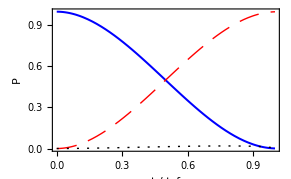

```mathematica
Plot[{sh10[t tf0],sh20[t tf0],sh20[t tf0](1-ct[t tf0]^2)},{t,0,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.005,0.02}]}},PlotRange->{All,Full},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t / t_f",FontSize->16,Italic],Style["P",FontSize->16,Italic]}]
```

```mathematica
FindMaximum[sh20[t tf0](1-ct[t tf0]^2),{t,0.8}]
```

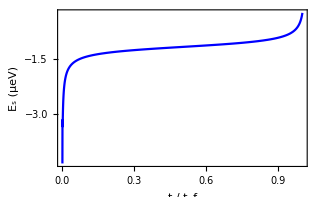

```mathematica
Plot[{fEs[t tf0]/(1.6 10^(-25))},{t,0.001,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.005,0.02}]},{Thick,Green},{Thick,Orange},{Thick,Black,Purple}},PlotRange->{All,Full},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t / t_f",FontSize->16,Italic],Style["E_s (μeV)",FontSize->16,Italic]}]
```

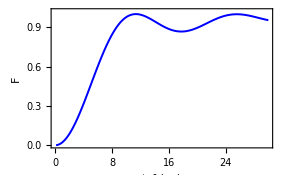

```mathematica
ListPlot[DFs,Joined->True,PlotStyle->{Thick,Blue,Thickness[0.005]},PlotRange->{All,{0,1.02}},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t_f (ns)",FontSize->16,Italic],Style["F",FontSize->16,Italic]}]
```

```mathematica
%%%%%%%%%
l: Dressaulhuas SOC 1ueV;tau:5ueV;u:3meV;
%%%%%%%%%%%%
```

```mathematica
g=1.35;muB=9.27 10^(-24);B=0.015;ET=-g muB B
```

-1.87718×10^-25

```mathematica
l=0.1 1.6 10^(-19) 10^(-6);
tau=5 1.6 10^(-19) 10^(-6);u=3000 1.6 10^(-19) 10^(-6);tf=11.5 10^(-9);hbar=1.055×10^(-34);
```

```mathematica
Est1[t_]=1/2(u+feps[t]+Sqrt[8 tau^2+(u+feps[t])^2]);Est[t_]=1/2(u+feps[t]-Sqrt[8 tau^2+(u+feps[t])^2]);
```

```mathematica
ct[t_]=-((feps[t]+u+√(8 tau^2+(u+feps[t])^2))/(√(8tau^2+(feps[t]+u+√(8tau^2+(feps[t]+u)^2))^2)));c1t[t_]=-((feps[t]+u-√(8 tau^2+(u+feps[t])^2))/(√(8tau^2+(feps[t]+u-√(8tau^2+(feps[t]+u)^2))^2)));
```

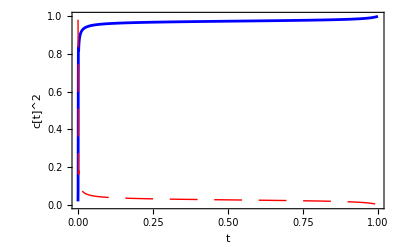

```mathematica
Plot[{ct[t tf]^2,c1t[t tf]^2},{t,0,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.01,0.025}]}},
PlotRange->{{0,1},{0,1}},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t",FontSize->20,Italic],Style["c[t]^2",FontSize->20]}]
```

```mathematica
H0[t_]={{ET, l/100,l /Sqrt[1-ct[t]^2]},{l/100,0,Sqrt[2]tau},{l/Sqrt[1-ct[t]^2],Sqrt[2]tau,u+feps[t]}};
```

```mathematica
E1[t_]=Eigenvalues[H0[t]][[1]];E2[t_]=Eigenvalues[H0[t]][[2]];
```

```mathematica
E3[t_]=Eigenvalues[H0[t]][[3]];
```

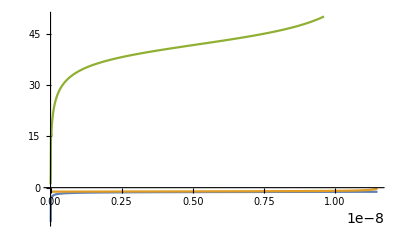

```mathematica
Plot[{E1[t]/(1.6 10^(-25)),E2[t]/(1.6 10^(-25)),E3[t]/(1.6 10^(-25))},{t,0,tf},PlotRange->{-10,50}]
```

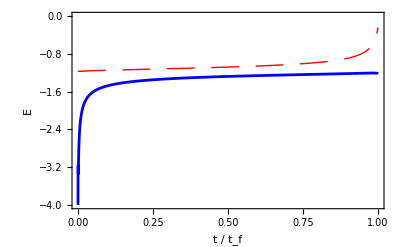

```mathematica
Plot[{E1[t tf]/(1.6 10^(-25)),E2[t tf]/(1.6 10^(-25))},{t,0.001,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.005,0.02}]},{Thick,Green},{Thick,Orange},{Thick,Black,Purple}},PlotRange->{All,{-4,0}},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t / t_f",FontSize->16,Italic],Style["E",FontSize->16,Italic]}]
```

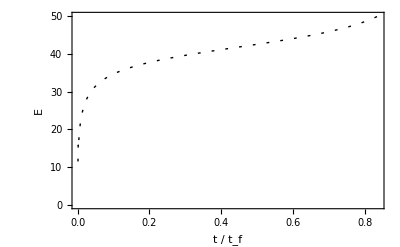

```mathematica
Plot[{E3[t tf]/(1.6 10^(-25))},{t,0.001,1},PlotStyle->{{Thick,Black,Dashing[{0.005,0.02}]},{Thick,Green},{Thick,Orange},{Thick,Black,Purple}},PlotRange->{All,{0,50}},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t / t_f",FontSize->16,Italic],Style["E",FontSize->16,Italic]}]
```

```mathematica
s3=NDSolve[{
I hbar h1'[t]==(ET h1[t]+ ( ct[t]/Sqrt[1-ct[t]^2]l/100+l) h2[t]+( c1t[t]/Sqrt[1-ct[t]^2]l/100+Sqrt[1-c1t[t]^2] l/Sqrt[1-ct[t]^2] )  h3[t]),
I hbar h2'[t]==( ( ct[t]/Sqrt[1-ct[t]^2]l/100+l)  h1[t]+fEs[t]h2[t]),
I hbar h3'[t]==(( c1t[t]/Sqrt[1-ct[t]^2]l/100+Sqrt[1-c1t[t]^2] l/Sqrt[1-ct[t]^2])  h1[t]+Est1[t] h3[t]),
h1[0]==1,h2[0]==0,h3[0]==0},{h1[t],h2[t],h3[t]},{t,0,tf},MaxSteps->∞];
sh31[t_]=Abs[h1[t]/.s3]^2;
sh32[t_]=Abs[h2[t]/.s3]^2;sh33[t_]=Abs[h3[t]/.s3]^2;
```

```mathematica
sh32[ tf] ct[tf]^2
```

{0.992374}

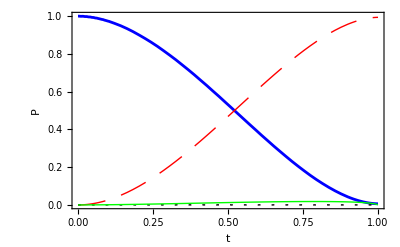

```mathematica
Plot[{sh31[t tf],sh32[t tf],sh33[t tf],sh32[t tf](1-(ct[t tf])^2)},{t,0,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.005,0.02}]},{Thick,Green}},PlotRange->{All,Full},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t ",FontSize->16,Italic],Style["P",FontSize->16,Italic]}]
```

```mathematica
FindMaximum[sh32[t tf](1-(ct[t tf])^2),{t,0.8}]
```

{0.0181258,{t→0.785343}}

```mathematica
s32=NDSolve[{
I hbar h1'[t]==ET h1[t]+ l/Sqrt[1-ct[t]^2]/100 h2[t]+ l /Sqrt[1-ct[t]^2]h3[t],
I hbar h2'[t]== l/Sqrt[1-ct[t]^2]/100 h1[t]+Sqrt[2]tau h3[t],
I hbar h3'[t]==  l/Sqrt[1-ct[t]^2] h1[t]+Sqrt[2]tau h2[t]+(feps[t]+u) h3[t],
h1[0]==1,h2[0]==0,h3[0]==0},{h1[t],h2[t],h3[t]},{t,0,tf},MaxSteps->∞];
sh12[t_]=Abs[h1[t]/.s32]^2;
sh22[t_]=Abs[h2[t]/.s32]^2;sh32[t_]=Abs[h3[t]/.s32]^2;
```

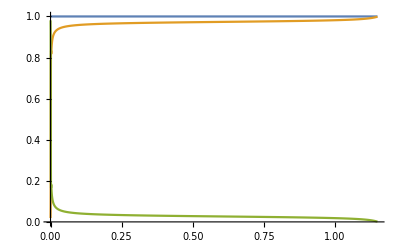

```mathematica
Plot[{c1t[t]^2+ct[t]^2,ct[t]^2,c1t[t]^2},{t,0,tf}]
```

```mathematica
sh22[tf]
```

{0.99106}

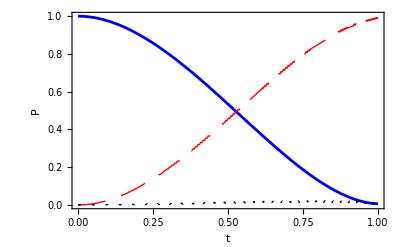

```mathematica
Plot[{sh12[t tf],sh22[t tf],sh32[t tf]},{t,0,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.005,0.02}]},{Thick,Green},{Thick,Orange},{Thick,Black,Purple}},PlotRange->{All,Full},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t ",FontSize->16,Italic],Style["P",FontSize->16,Italic]}]
```